Parameterized Assymetry from gydep

```mathematica
(*SetDirectory["C:\\Users\\prajwal\\Dropbox\\MEP\\GEANT_Analysis"]*)
SetDirectory["/home/prajwal/Dropbox/MEP/GEANT_Analysis"]
```

/home/prajwal/Dropbox/MEP/GEANT_Analysis

```mathematica
Clear[PlotLegend]
<<PlotLegends`
Needs["ErrorBarPlots`"]
```

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
gydep = ReadList["spinlight_gydep4.dat",{Real,Real,Real,Real,Real,Real,Real,Real}];
```

1000

9.86944×10^-7+0.0000524483 x-0.0000206675 x^2+5.76616×10^-6 x^3-6.46704×10^-7 x^4

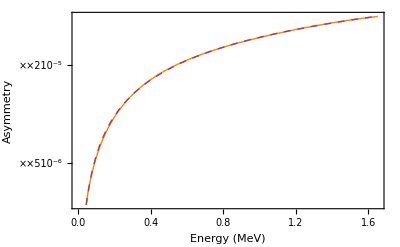

```mathematica
gydepL=Dimensions[gydep][[1]]
gydepAsym=Table[{gydep[[k]][[2]],gydep[[k]][[5]]},{k,1,gydepL}];
gydepPoly = Fit[gydepAsym,{1,x,x^2,x^3,x^4},x]
gydepP1dat=Table[{x,gydepPoly},{x,gydep[[1]][[2]],gydep[[gydepL]][[2]],gydep[[2]][[2]]-gydep[[1]][[2]]}];
ListLogPlot[{gydepP1dat/2,gydepAsym/2},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","Asymmetry"},PlotStyle->{Orange,Dashed},PlotLegend->{"5GeV @ 0.22T","12GeV @ 0.5T"}]
```

```mathematica
Clear[write1]
write1=OpenWrite["asym_new.dat"]
WriteString[write1,"# E (MeV)" ,"|" ,"5GeV @ 0.22T","|","12GeV @ 0.5T","\n"];
For[i=10,i≤gydepL,i++,
WriteString[write1,AccountingForm[SetPrecision[gydepAsym[[i]][[1]]/2,8]]," " ,AccountingForm[SetPrecision[gydepP1dat[[i]][[2]]/2,8]]," ",AccountingForm[SetPrecision[gydepAsym[[i]][[2]]/2,8]],"\n"];
];
Close[write1]
```

OutputStream[asym_new.dat,299]

asym_new.dat

```mathematica
gydep[[1000]][[2]]
```

3.309

\Delta Asym (Modelled Asym - Physics Asym)

{1000,8}

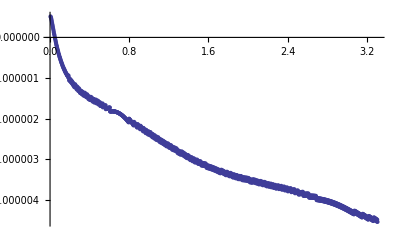

```mathematica
TestSize=Dimensions[gydep]
TestPlotA=Table[{gydep[[k]][[2]],gydepP1dat[[k]][[2]]-gydepAsym[[k]][[2]]},{k,1,gydepL}];
ListPlot[TestPlotA,PlotRange->Full]
```

```mathematica
Clear[write1]
write1=OpenWrite["deltaasym.dat"]
WriteString[write1,"# E (MeV)" ,"|" ,"Delta_Asym","\n"];
For[i=10,i≤gydepL,i++,
WriteString[write1,AccountingForm[SetPrecision[TestPlotA[[i]][[1]],11]],"\t" ,AccountingForm[SetPrecision[TestPlotA[[i]][[2]],11]],"\n"];
];
Close[write1]
```

OutputStream[deltaasym.dat,875]

deltaasym.dat

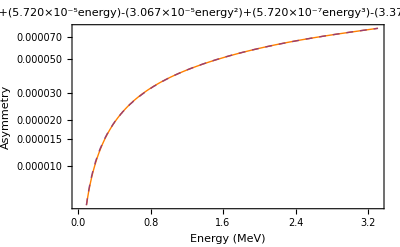

```mathematica
Asym[x_]=0.00005720464766833081 x-0.00003067509392850383 x^2+0.000013807388901810283 x^3-3.375222926815788*^-6 x^4+3.293470979419155*^-7 x^5
Asym[0]
```

0.0000572046 x-0.0000306751 x^2+0.0000138074 x^3-3.37522×10^-6 x^4+3.29347×10^-7 x^5

0.

Parameterized N(SR) from gydep

```mathematica
SetDirectory["C:\\Users\\prajwal\\Dropbox\\MEP\\GEANT_Analysis"]
(*SetDirectory["/home/prajwal/Dropbox/MEP/GEANT_Analysis"]*)
```

C:\Users\prajwal\Dropbox\MEP\GEANT_Analysis

```mathematica
gydep = ReadList["spinlight_gydep4.dat",{Real,Real,Real,Real,Real,Real,Real,Real}];
```

1000

FittedModel[1.42756×10^11-(3.00196×10^8)/x^2+(8.50428×10^10)/x-2.32143×10^11 x+6.04918×10^10 x^2]

InterpolatingFunction[{{0.005,3.309}},<>]

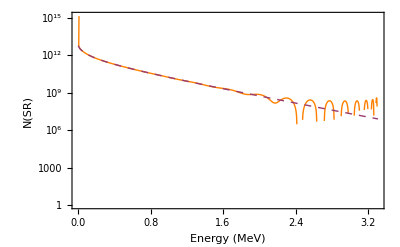

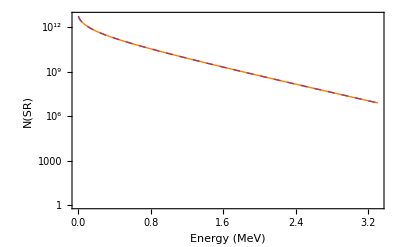

```mathematica
gydepL=Dimensions[gydep][[1]]
gydepAsym=Table[{gydep[[k]][[2]],gydep[[k]][[3]]},{k,1,gydepL}];
gydepPoly = Fit[gydepAsym, Table[x^k,{k,-120,120}],x];
nlm2=NonlinearModelFit[gydepAsym, a+b x+c x^2+d/x+e/x^2,{a,b,c,d,e},x]
nlm=Interpolation[gydepAsym]
gydepP1dat=Table[{x,gydepPoly},{x,gydep[[1]][[2]],gydep[[gydepL]][[2]],gydep[[2]][[2]]-gydep[[1]][[2]]}];
gydepP1dat2=Table[{x,nlm[x]},{x,gydep[[1]][[2]],gydep[[gydepL]][[2]],gydep[[2]][[2]]-gydep[[1]][[2]]}];
ListLogPlot[{gydepP1dat,gydepAsym},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","N(SR)"},PlotStyle->{Orange,Dashed},PlotLegend->{"Parameterized N(SR) Fit","GEANT4 N(SR)"}]
ListLogPlot[{gydepP1dat2,gydepAsym},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","N(SR)"},PlotStyle->{Orange,Dashed},PlotLegend->{"Parameterized N(SR) Fit","GEANT4 N(SR)"}]
```

```mathematica
nlm2[0.000001]
```

-3.00111×10^20

```mathematica
LogPlot[nlm[xx/10^6],{xx,1,10},Frame-> True,FrameLabel->{"Photon Energy (eV)","N(SR)"},PlotLabel->"Simple number of SR Photons / Photon Energy",PlotLegend->{"E_e=10GeV,  B_wig=4T,  θ_SR=10mrad"}]
```

InterpolatingFunction::dmval: Input value {1.00018×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

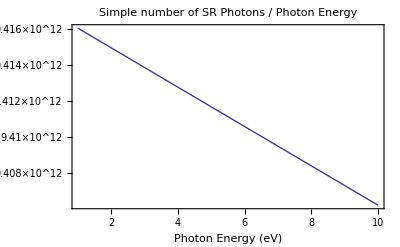

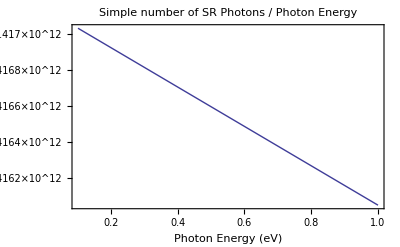

```mathematica
LogPlot[nlm[xx],{xx,0,3},Frame-> True,FrameLabel->{"Photon Energy (eV)","N(SR)"},PlotLabel->"Simple number of SR Photons / Photon Energy",PlotLegend->{"E_e=10GeV,  B_wig=4T,  θ_SR=10mrad"}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

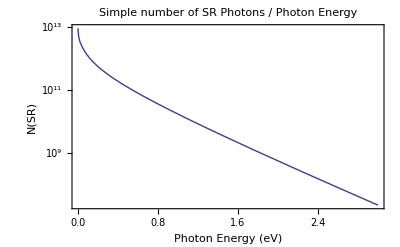

```mathematica
Table[NIntegrate[nlm[xx],{xx,0.000001,k}],{k,
```

4.57802×10^11

Parameterized N(SL) from gydep

```mathematica
(*SetDirectory["C:\\Users\\prajwal\\Dropbox\\MEP\\GEANT_Analysis"]*)
SetDirectory["/home/prajwal/Dropbox/MEP/GEANT_Analysis"]
```

C:\Users\prajwal\Desktop

```mathematica
gydep = ReadList["spinlight_gydep4.dat",{Real,Real,Real,Real,Real,Real,Real,Real}];
```

1000

-114153.+(7.65461×10^-52)/x^30+(1.49278×10^-49)/x^29+(2.86916×10^-47)/x^28+(5.37448×10^-45)/x^27+(9.62194×10^-43)/x^26+(1.57924×10^-40)/x^25+(2.12476×10^-38)/x^24+(1.27839×10^-36)/x^23-(5.67329×10^-34)/x^22-(3.2556×10^-31)/x^21-(1.13523×10^-28)/x^20-(3.14945×10^-26)/x^19-(7.03092×10^-24)/x^18-(1.10981×10^-21)/x^17-(4.04295×10^-20)/x^16+(4.36685×10^-17)/x^15+(1.44725×10^-14)/x^14+(1.04784×10^-12)/x^13-(5.80939×10^-10)/x^12-(8.57081×10^-8)/x^11+0.0000367955/x^10-0.00468617/x^9+0.325451/x^8-14.0116/x^7+389.43/x^6-6996.8/x^5+78858.5/x^4-517115./x^3+(1.61147×10^6)/x^2-337217./x

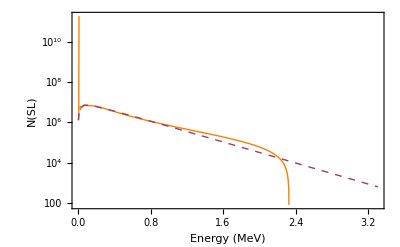

```mathematica
gydepL=Dimensions[gydep][[1]]
gydepAsym=Table[{gydep[[k]][[2]],gydep[[k]][[4]]},{k,1,gydepL}];
gydepPoly = Fit[gydepAsym,Table[x^-k,{k,0,30}],x]
gydepP1dat=Table[{x,gydepPoly},{x,gydep[[1]][[2]],gydep[[gydepL]][[2]],gydep[[2]][[2]]-gydep[[1]][[2]]}];
ListLogPlot[{gydepP1dat,gydepAsym},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","N(SL)"},PlotStyle->{Orange,Dashed},PlotLegend->{"Parameterized N(SL) Fit","GEANT4 N(SL)"}]
```

Geant4: N (SR, Spin-Light) vs. E

```mathematica
(*SetDirectory["C:\\Users\\prajwal\\Dropbox\\MEP\\GEANT_Analysis"]*)
SetDirectory["/home/prajwal/Dropbox/MEP/GEANT_Analysis"]
Directory[]
```

/home/prajwal/Dropbox/MEP/GEANT_Analysis

/home/prajwal/Dropbox/MEP/GEANT_Analysis

```mathematica
g4srsl0=Import["SpinICTest_SpinIC.csv"];
g4srsl0L=Dimensions[g4srsl0][[1]]
```

18902

```mathematica
g4srsl0e=Table[g4srsl0[[k]][[1]],{k,1,g4srsl0L}];
(*Histogram[g4srsl0e,ScalingFunctions->{None,"Log"},Frame-> True,FrameLabel->{"Energy (MeV)","N (SR)"}]*)
```

```mathematica
g4srsl0ehistl=0.0001;
g4srsl0ehistu=.4;
g4srsl0ehisti=0.001;
g4srsl0ehists=10^5;
g4srsl0ebinc=BinCounts[g4srsl0e,{g4srsl0ehistl,g4srsl0ehistu,g4srsl0ehisti}];
g4srsl0ebincn=Dimensions[g4srsl0ebinc][[1]];
g4srehist=Table[{g4srsl0ehistl+(g4srsl0ehisti×(k-1)),g4srsl0ehists×g4srsl0ebinc[[k]]},{k,1,g4srsl0ebincn}];
g4slehist=Table[{g4srsl0ehistl+(g4srsl0ehisti×(k-1)),g4srsl0ehists×Asym[g4srsl0ehistl+(g4srsl0ehisti×(k-1))]×g4srsl0ebinc[[k]]},{k,1,g4srsl0ebincn}];
```

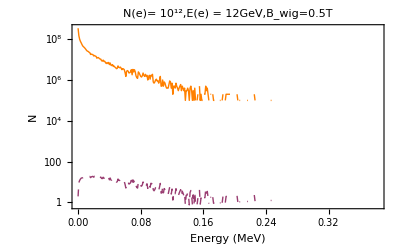

```mathematica
ListLogPlot[{g4srehist,g4slehist},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","N"},PlotStyle->{Orange,Dashed},PlotLegend->{"GEANT4 N(SR)","GEANT4 N(SL)"},PlotLabel->"N(e)= 10^12,E(e) = 12GeV,B_wig=0.5T"]
```

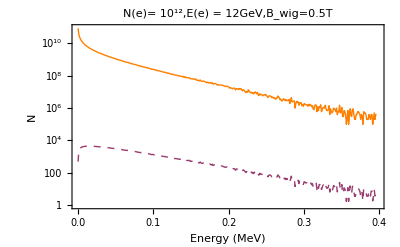

```mathematica
Clear[write1]
write1=OpenWrite["nslsr_new_12GeV0.5T.dat"]
WriteString[write1,"# N(e)= 10^12, B_wig=0.5T, E_beam=12GeV, Δθ = 20mrad","\n","# E (MeV)" ,"\t |" ,"Number(SR)","|","Number(SL)","\n"];
For[i=1,i≤g4srsl0ebincn,i++,
WriteString[write1,AccountingForm[SetPrecision[g4srehist[[i]][[1]],10]],"\t" ,AccountingForm[SetPrecision[g4srehist[[i]][[2]],10]],"\t",AccountingForm[Round[SetPrecision[g4slehist[[i]][[2]],10]]],"\n"];
];
Close[write1]
```

OutputStream[nslsr_new_12GeV0.5T.dat,150]

AccountingForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of AccountingForm :: sigz will be suppressed during this calculation.

nslsr_new_12GeV0.5T.dat

Geant4: Power (SR, Spin-Light) vs. E

```mathematica
g4srpower=Table[0,{k,1,g4srsl0ebincn}];
g4slpower=Table[0,{k,1,g4srsl0ebincn}];
g4srsl0powers=500;
For[ii=1,ii≤g4srsl0ebincn,ii++,
g4srpower[[ii]]=g4srehist[[ii]][[1]]×g4srehist[[ii]][[2]];
g4slpower[[ii]]=g4slehist[[ii]][[1]]×g4slehist[[ii]][[2]];
];
g4psrehist=Table[{g4srsl0ehistl+(g4srsl0ehisti×(k-1)),g4srpower[[k]]/g4srsl0powers},{k,1,g4srsl0ebincn}];
g4pslehist=Table[{g4srsl0ehistl+(g4srsl0ehisti×(k-1)),g4slpower[[k]]*100},{k,1,g4srsl0ebincn}];
```

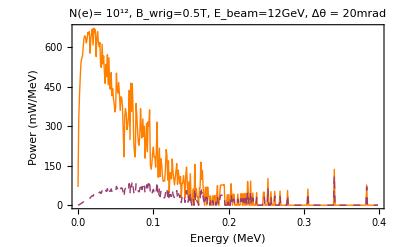

```mathematica
ListPlot[{g4psrehist,g4pslehist},Joined->True,Frame-> True,FrameLabel->{"Energy (MeV)","Power (mW/MeV)"},PlotStyle->{Orange,Dashed},PlotLegend->{"GEANT4 P_SR","GEANT4 P_SL×50k"},PlotLabel->"N(e)= 10^12, B_wrig=0.5T, E_beam=12GeV, Δθ = 20mrad",PlotRange->Full]
```

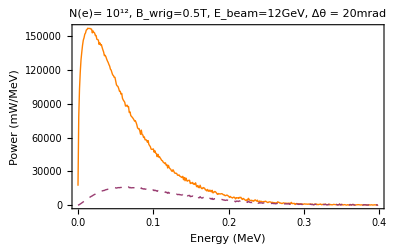

```mathematica
Clear[write1]
write1=OpenWrite["pslsr_new_0.5T12GeV.dat"]
WriteString[write1,"# N(e)= 10^12, B_wig=0.5T, E_beam=12GeV, Δθ = 20mrad","\n","# E (MeV)" ,"\t |" ,"SRPower (mW/MeV)","|","SLPower (mW/MeV) X 50k","\n"];
For[i=1,i≤g4srsl0ebincn,i++,
WriteString[write1,AccountingForm[SetPrecision[g4psrehist[[i]][[1]],10]],"\t" ,AccountingForm[SetPrecision[g4psrehist[[i]][[2]],10]],"\t",AccountingForm[SetPrecision[g4pslehist[[i]][[2]],10]],"\n"];
];
Close[write1]
```

OutputStream[pslsr_new_0.5T12GeV.dat,173]

pslsr_new_0.5T12GeV.dat

Ionization at IC2

```mathematica
(*SetDirectory["C:\\Users\\prajwal\\Desktop"];*)
SetDirectory["/home/prajwal/Dropbox/MEP/GEANT_Analysis"]
Directory[]
```

C:\Users\prajwal\Desktop

```mathematica
g4ICidata1=Import["ICi100k4p5m.csv"];
g4ICidataL1=Dimensions[g4ICidata1][[1]]
g4ICidata2=Import["ICi100k31m.csv"];
g4ICidataL2=Dimensions[g4ICidata2][[1]]
g4ICidata3=Import["ICi100k22m.csv"];
g4ICidataL3=Dimensions[g4ICidata3][[1]]
```

751784

971566

1267040

```mathematica
g4ICiBin1=BinCounts[Table[g4ICidata1[[k]][[9]],{k,1,g4ICidataL1}],{40,60,1}];
g4ICiBinn1=20;
g4ICiBin2=BinCounts[Table[g4ICidata2[[k]][[9]],{k,1,g4ICidataL2}],{40,60,1}];
g4ICiBinn2=20;
g4ICiBin3=BinCounts[Table[g4ICidata3[[k]][[9]],{k,1,g4ICidataL3}],{40,60,1}];
g4ICiBinn3=20;
```

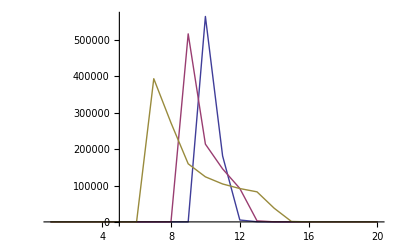

```mathematica
g4ICihist1 = Table[{k,g4ICiBin1[[k]]},{k,1,g4ICiBinn1}];
g4ICihist2 = Table[{k,g4ICiBin2[[k]]},{k,1,g4ICiBinn2}];
g4ICihist3 = Table[{k,g4ICiBin3[[k]]},{k,1,g4ICiBinn3}];
ListLinePlot[{g4ICihist1,g4ICihist2,g4ICihist3},PlotRange->Full]
```

```mathematica
Clear[write1]
write1=OpenWrite["satCurrent.dat"]
WriteString[write1,"# t (s)" ,"\t |" ,"0.5m:I/e (A/e)","|","1.0m:I/e (A/e)","|","2.0m:I/e (A/e)","\n"];
For[i=1,i≤g4ICiBinn3,i++,
WriteString[write1,AccountingForm[SetPrecision[g4ICihist3[[i]][[1]],10]],"\t" ,AccountingForm[SetPrecision[g4ICihist1[[i]][[2]],10]],"\t",AccountingForm[SetPrecision[g4ICihist2[[i]][[2]],10]],"\t",AccountingForm[SetPrecision[g4ICihist3[[i]][[2]],10]],"\n"];
];
Close[write1]
```

OutputStream[satCurrent.dat,121]

satCurrent.dat

No. other events (-SR Events)
(icnum==3 && Pos.z()/m >= -5.5)

```mathematica
g4notsr=Import["N-SR.csv"];
g4notsrL=Dimensions[g4notsr][[1]]
```

248877

30

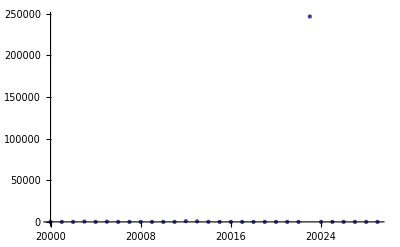

```mathematica
g4notsrbinc=BinCounts[Table[g4notsr[[k]][[8]],{k,1,g4notsrL}],{20000,20030,1}];
g4notsrbincL=Dimensions[g4notsrbinc][[1]]
g4notsrlist=Table[{20000+k-1,g4notsrbinc[[k]]},{k,1,g4notsrbincL}];
ListPlot[g4notsrlist,PlotRange->Full]
```

```mathematica
Clear[write1]
write1=OpenWrite["notSR.dat"]
WriteString[write1,"#N_{tot} = 10^6","\n","#20002: EM Ionisation \n","# 20003: EM Bremsstrahlung \n","# 20004: EM Pair production by charged particle \n","# 20005: EM Annihilation \n","# 20012: EM PhotoElectric Effect \n",
"# 20013: EM Compton Scattering \n","# 20014: EM Gamma Conversion \n"];
WriteString[write1,"# EventID" ,"\t |" ,"N","\n"];
For[i=1,i≤g4notsrbincL,i++,
WriteString[write1,AccountingForm[SetPrecision[g4notsrlist[[i]][[1]],10]],"\t",AccountingForm[SetPrecision[g4notsrlist[[i]][[2]],10]],"\n"];
];
Close[write1]
```

OutputStream[notSR.dat,63]

notSR.dat

Locations in IC
(icnum==2)

```mathematica
g4overlap=Import["SpinICTest_SpinIC.csv"];
g4overlapL=Dimensions[g4overlap][[1]]
```

57029

```mathematica
g4od2bincx=Table[g4overlap[[k]][[2]],{k,1,g4overlapL}];
g4od2bincy=Table[g4overlap[[k]][[3]],{k,1,g4overlapL}];
g4od2bincminx=Min[g4od2bincx]
g4od2bincmaxx=Max[g4od2bincx]
g4od2bincminy=Min[g4od2bincy]
g4od2bincmaxy=Max[g4od2bincy]
```

0.039

0.303148

-0.107625

0.195664

```mathematica
g4od2bincint=.001
g4od2binc=BinCounts[Table[{g4overlap[[k]][[2]],g4overlap[[k]][[3]]},{k,1,g4overlapL}],{g4od2bincminx,g4od2bincmaxx,g4od2bincint},{g4od2bincminy,g4od2bincmaxy,g4od2bincint}];
g4od2bincL=Dimensions[g4od2binc]
g4od2hist=Table[{0,0,0},{k,1,g4od2bincL[[2]]×g4od2bincL[[1]]}];
g4od2histcount=1;
g4asymcouP=0;
g4asymcouN=0;
For[k=1,k<=g4od2bincL[[1]],k++,
For[l=1,l<=g4od2bincL[[2]],l++,
g4od2hist[[g4od2histcount]]={g4od2bincint/2+g4od2bincminx + ((k-1)×g4od2bincint)-(0.04),(g4od2bincint/2+g4od2bincminy + ((l-1)×g4od2bincint))/10,g4od2binc[[k]][[l]]};
];
```

```mathematica
g4asymSize=10;
g4asym=Table[0,{k,1,g4asymSize}];
For[m=1,m≤g4asymSize,m++,
g4od2bincint=.0001×2^m;
g4od2binc=BinCounts[Table[{g4overlap[[k]][[2]],g4overlap[[k]][[3]]},{k,1,g4overlapL}],{g4od2bincminx,g4od2bincmaxx,g4od2bincint},{g4od2bincminy,g4od2bincmaxy,g4od2bincint}];
g4od2bincL=Dimensions[g4od2binc];
g4asymcouP=0;
g4asymcouN=0;
For[k=1,k<=g4od2bincL[[1]],k++,
For[l=1,l<=g4od2bincL[[2]],l++,
If[(g4od2bincint/2+g4od2bincminy + ((l-1)×g4od2bincint))/10≥0, g4asymcouP+=g4od2binc[[k]][[l]],g4asymcouN+=g4od2binc[[k]][[l]]];
];
];
g4asym[[m]]=N[Abs[g4asymcouP-g4asymcouN]/(g4asymcouP+g4asymcouN)];
];
g4asym
```

{0.0121645,0.0121645,0.216872,0.241658,0.534223,0.534223,0.919393,0.919393,0.919393,0.921032}

InterpolatingFunction[{{2., 1024.}}, <>]

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

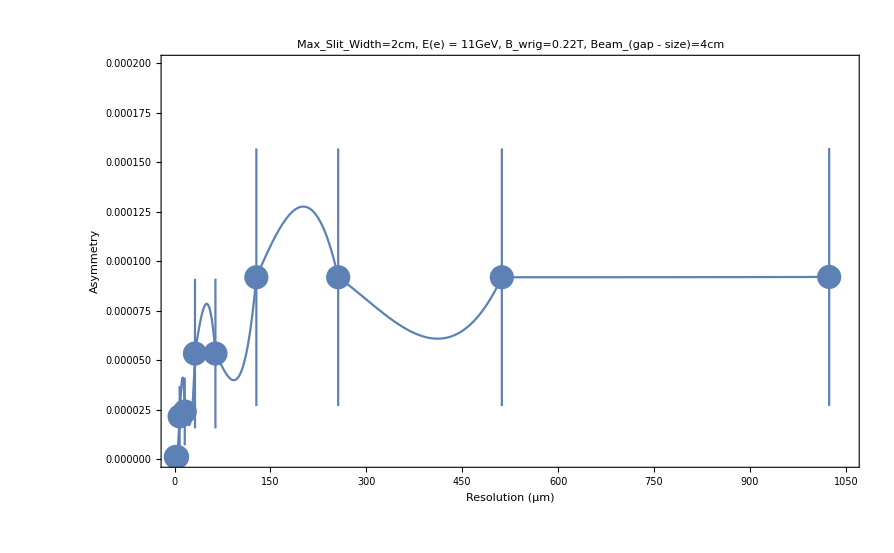

```mathematica
g4asymsmooth=Interpolation[Table[{2^k,g4asym[[k]]×10^-4},{k,1,g4asymSize}]]
g4asympt=Table[{{2^k,g4asym[[k]]×10^-4},ErrorBar[(g4asym[[k]]×10^-4)/(√2)]},{k,1,g4asymSize}];
g4asymptsmooth=Table[{k,g4asymsmooth[k]},{k,1,2^g4asymSize,1}];
Show[{ListPlot[g4asymptsmooth,Joined->True,PlotRange->{{0,1050},{0,2×10^-4}},Frame->True,FrameLabel->{"Resolution (μm)","Asymmetry"},PlotLabel->"Max_Slit_Width=2cm, E(e) = 11GeV, B_wrig=0.22T, Beam_(gap - size)=4cm"],ErrorListPlot[g4asympt,PlotRange->{{0,1050},{0,2×10^-4}},Frame->True,FrameLabel->{"Resolution (μm)","Asymmetry"},PlotLabel->"Max_Slit_Width=2cm, E(e) = 11GeV, B_wrig=0.22T, Beam_(gap - size)=4cm"]}]
```

```mathematica
Clear[write1]
write1=OpenWrite["asymR.dat"]
WriteString[write1,"Max_Slit_Width=2cm, E(e) = 11GeV, B_wrig=0.22T, Beam_gap-size=4cm","\n","#"];
WriteString[write1,"# Resolution (μm)" ,"\t |" ,"Asymmetry","\t |" ,"ErrorBars","\n"];
For[i=1,i≤g4asymSize,i++,
WriteString[write1,AccountingForm[SetPrecision[g4asympt[[i]][[1]][[1]],7]],"\t",AccountingForm[SetPrecision[g4asympt[[i]][[1]][[2]]*100,7]],"\t",AccountingForm[SetPrecision[(g4asym[[i]]×10^-2)/(√2),7]],"\n"];
];
Close[write1]
```

OutputStream[…]

asymR.dat

```mathematica
g4asympt[[10]][[1]][[2]]
```

0.0000921032

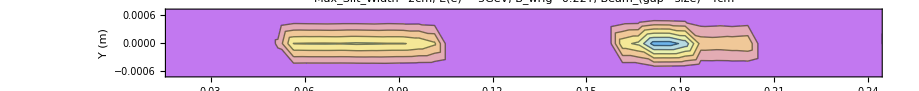

```mathematica
ListContourPlot[g4od2hist,PlotRange->{{0.02,.240},{-.0007,.0007}},Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Max_Slit_Width=2cm, E(e) = 5GeV, B_wrig=0.22T, Beam_(gap - size)=4cm",ColorFunction->"Pastel",AspectRatio->(0.02/.2)]
```

Projections onto X & Y axis

```mathematica
g4od2binc=BinCounts[Table[{g4overlap[[k]][[2]],g4overlap[[k]][[3]]},{k,1,g4overlapL}],{g4od2bincminx,g4od2bincmaxx,g4od2bincint},{g4od2bincminy,g4od2bincmaxy,g4od2bincint}];
g4od2bincL=Dimensions[g4od2binc]
g4od2hist=Table[{0,0,0},{k,1,g4od2bincL[[2]]×g4od2bincL[[1]]}];
g4od2histcount=1;
For[k=1,k<=g4od2bincL[[1]],k++,
For[l=1,l<=g4od2bincL[[2]],l++,
g4od2histx=g4od2bincint/2+g4od2bincminx + ((k-1)×g4od2bincint);
g4od2histy=g4od2bincint/2+g4od2bincminy + ((l-1)×g4od2bincint);
(*If[g4od2histx≤0.9,
g4od2hist[[g4od2histcount]]={g4od2histx,g4od2histy,g4od2binc[[k]][[l]]};
If[g4od2histx≤0.04 && Abs[g4od2histy]≤0.02,
g4od2hist[[g4od2histcount]]={g4od2histx,g4od2histy,0.0};
];,
g4od2hist[[g4od2histcount]]={g4od2histx,g4od2histy,0.5*g4od2binc[[k]][[l]]}
];*)
g4od2hist[[g4od2histcount]]={g4od2histx/10,g4od2histy,g4od2binc[[k]][[l]]};
g4od2histcount++;
];
];
```

{24,24}

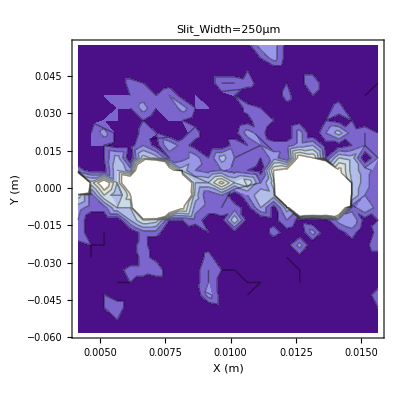

```mathematica
ListContourPlot[g4od2hist,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Slit_Width=250μm"]
```

```mathematica
Clear[write1]
write1=OpenWrite["overlap100.dat"]
WriteString[write1,"#N_{tot} = 10^5","\n","#"];
WriteString[write1,"# X" ,"\t |" ,"Y","\t |" ,"N","\n"];
For[i=1,i≤g4od2histcount-1,i++,
WriteString[write1,AccountingForm[SetPrecision[g4od2hist[[i]][[1]],7]],"\t",AccountingForm[SetPrecision[g4od2hist[[i]][[2]],7]],"\t",AccountingForm[SetPrecision[g4od2hist[[i]][[3]],7]],"\n"];
];
Close[write1]
```

OutputStream[overlap100.dat,263]

overlap100.dat

```mathematica
;
```

Y_1D Projection

```mathematica
g4od2dat=Table[{0,0,0},{k,1,g4od2bincL[[1]]}];
For[l=1,l<=g4od2bincL[[1]],l++,
g4od2projx = 0;
For[k=1,k<=g4od2bincL[[2]],k++,
g4od2projx+=g4od2binc[[l]][[k]];
];
g4od2dat[[l]]=g4od2projx;
];
```

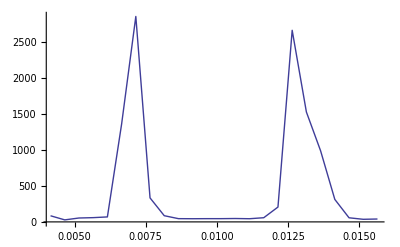

```mathematica
g4od2projhist=Table[{(g4od2bincint/2+g4od2bincminx + ((k-1)×g4od2bincint))/10,g4od2dat[[k]]},{k,1,g4od2bincL[[2]]}];
ListLinePlot[g4od2projhist,PlotRange->Full]
```

```mathematica
N[g4od2projhist[[11]]]
```

{0.0915005,53.}

```mathematica
Clear[write1]
write1=OpenWrite["overlap100Y.dat"]
WriteString[write1,"#N_{tot} = 10^5","\n","#"];
WriteString[write1,"# Y" ,"\t |" ,"N","\n"];
For[i=1,i≤g4od2bincL[[2]],i++,
WriteString[write1,AccountingForm[SetPrecision[g4od2projhist[[i]][[1]],7]],"\t",AccountingForm[SetPrecision[g4od2projhist[[i]][[2]],7]],"\n"];
];
Close[write1]
```

OutputStream[overlap100Y.dat,217]

overlap100Y.dat

X_1D Projection

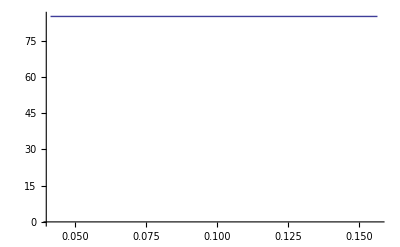

```mathematica
(*Scale to match height*)
g4od2dat=Table[{0,0,0},{k,1,g4od2bincL[[1]]}];
For[l=1,l<=g4od2bincL[[2]],l++,
g4od2projx = 0;
For[k=1,k<=g4od2bincL[[1]],k++,
g4od2projx+=g4od2binc[[1]][[k]];
];
g4od2dat[[l]]=g4od2projx;
];
g4od2projhist=Table[{g4od2bincint/2+g4od2bincminx + ((k-1)×g4od2bincint),g4od2dat[[k]]},{k,1,g4od2bincL[[2]]}];
ListLinePlot[g4od2projhist,PlotRange->Full]
```

```mathematica
Clear[write1]
write1=OpenWrite["overlap100X.dat"]
WriteString[write1,"#N_{tot} = 10^5","\n","#"];
WriteString[write1,"# X" ,"\t |" ,"N","\n"];
For[i=1,i≤g4od2bincL[[2]],i++,
WriteString[write1,AccountingForm[SetPrecision[g4od2projhist[[i]][[1]],7]],"\t",AccountingForm[SetPrecision[g4od2projhist[[i]][[2]],7]],"\n"];
];
Close[write1]
```

OutputStream[overlap100X.dat,189]

overlap100X.dat

```mathematica
(*for 2D overlap*)
```

!Testing Code!

```mathematica
aaa={{1,2,3},{4,5,6},{7,8,9}}
aaaa=Transpose[aaa]
aaaa[[2]][[]]
{{on,yt}}=Position[aaaa,6]
aaa[[yt]][[on]]
```

{{1,2,3},{4,5,6},{7,8,9}}

{{1,4,7},{2,5,8},{3,6,9}}

{2,5,8}

{{3,2}}

6

```mathematica
Export["testing.png",Plot[Sin[x],{x,0,3.14}]];
```

```mathematica
aaa={{1,2},{1,3},{2,3},{2,3}}
aaanext=BinCounts[aaa,{0,4,1},{0,4,1}]
aaanext[[3]][[4]]
```

{{1,2},{1,3},{2,3},{2,3}}

{{0,0,0,0},{0,0,1,1},{0,0,0,2},{0,0,0,0}}

2